```mathematica
IF[x_]:=(Sin[(((2*x^2)+1)*Pi^2*0.25)^0.5])^2
```

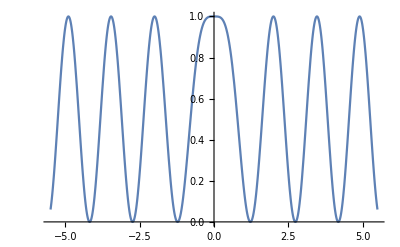

```mathematica
Plot[IF[x],{x,-5.5,5.5}]
```

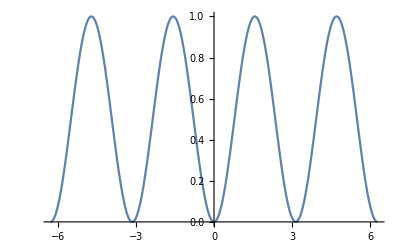

```mathematica
Plot[(Sin[x])^2,{x,-2*Pi,2*Pi}]
```

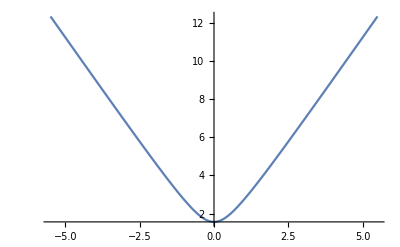

```mathematica
TE[x_]:=(((2*x^2)+1)*Pi^2*0.25)^0.5
Plot[TE[x],{x,-5.5,5.5}]
```

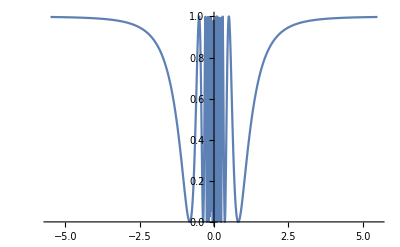

```mathematica
IF2[x_]:=(Sin[(((2*x^-2)+1)*Pi^2*0.25)^0.5])^2
Plot[IF2[x],{x,-5.5,5.5}]
```

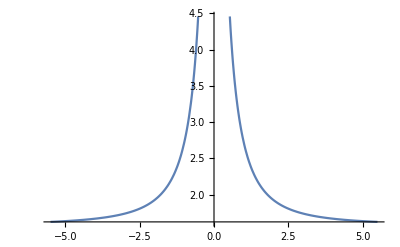

```mathematica
TE[x_]:=(((2*x^-2)+1)*Pi^2*0.25)^0.5
Plot[TE[x],{x,-5.5,5.5}]
```

```mathematica
FID[x_]:=(Cos[2*x])^2+2*Cos[x]*Cos[2*x]
```

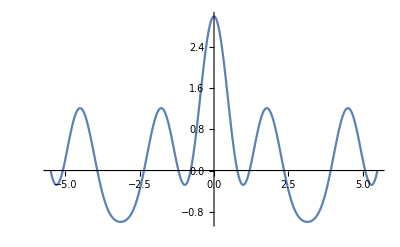

```mathematica
Plot[FID[x],{x,-5.5,5.5}]
```

```mathematica
Table[PauliMatrix[k]//MatrixForm,{k,3}]
```

{(0 | 1
1 | 0),(0 | -ⅈ
ⅈ | 0),(1 | 0
0 | -1)}

```mathematica
M = PauliMatrix[1]
```

{{0,1},{1,0}}

```mathematica
MatrixExp[M]
```

{{1/(2 ⅇ)+ⅇ/2,-1/(2 ⅇ)+ⅇ/2},{-1/(2 ⅇ)+ⅇ/2,1/(2 ⅇ)+ⅇ/2}}

```mathematica
M= {{0,Exp[ⅈat]},{Exp[-ⅈat],0}}
```

{{0,ⅇ^ⅈat},{ⅇ^-ⅈat,0}}

```mathematica
Eigensystem[M]
```

{{-1,1},{{-ⅇ^ⅈat,1},{ⅇ^ⅈat,1}}}

```mathematica
Fid[a_]:=(8 +2*(Cos[Sqrt[(π*0.5)^2*(2*a^2+1)]])^2*(1+Cos[Sqrt[2]*a*π])+0.5*((2*Sqrt[2]*a^2)/(2*Sqrt[2]*a^2+1))*(Sin[Sqrt[(π*0.5)^2*(2*a^2+1)]])^2*(1-Cos[Sqrt[2]*a*π])+2*((2*Sqrt[2]*a^2)/(2*Sqrt[2]*a^2+1))^0.5*Sin[2*Sqrt[(π*0.5)^2*(2*a^2+1)]]*Sin[Sqrt[2]*a*π]+8*Cos[Sqrt[(π*0.5)^2*(2*a^2+1)]]*Cos[(a*π)/Sqrt[2]]+4*((2*Sqrt[2]*a^2)/(2*Sqrt[2]*a^2+1))^0.5*Sin[Sqrt[(π*0.5)^2*(2*a^2+1)]]*Sin[(a*π)/Sqrt[2]])*1/20
```

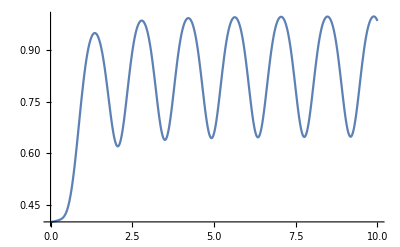

```mathematica
Plot[Fid[a],{a,0,10}]
```

```mathematica
m=1
B1=1
t=m*Sqrt[2]*π/B1
```

1

1

√2 π

```mathematica
Fid1[A_]:=(4+(Abs[Exp[ⅈ*0.5*A*t]*(Cos[((0.5*A)^2+(B1*0.5/Sqrt[2])^2)^0.5 *t]+ⅈ*0.5*A*((0.5*A)^2+(B1*0.5/Sqrt[2])^2)^-0.5*Sin[((0.5*A)^2+(B1*0.5/Sqrt[2])^2)^0.5*t])+Exp[-ⅈ*0.5*A*t]*(Cos[((0.5*A)^2+(B1*0.5/Sqrt[2])^2)^0.5 *t]-ⅈ*0.5*A*((0.5*A)^2+(B1*0.5/Sqrt[2])^2)^-0.5*Sin[((0.5*A)^2+(B1*0.5/Sqrt[2])^2)^0.5*t])+2])^2)/20
```

```mathematica
Fid3[a_]:=0.05*(4+Abs[Exp[ⅈ *π*a/Sqrt[2]]*(Cos[Sqrt[(π*0.5)^2*(2*a^2+1)]]+ⅈ*0.5*((2*Sqrt[2]*a^2)/(2*Sqrt[2]*a^2+1))^0.5*Sin[Sqrt[(π*0.5)^2*(2*a^2+1)]])+Exp[-ⅈ *π*a/Sqrt[2]]*(Cos[Sqrt[(π*0.5)^2*(2*a^2+1)]]-ⅈ*0.5*((2*Sqrt[2]*a^2)/(2*Sqrt[2]*a^2+1))^0.5*Sin[Sqrt[(π*0.5)^2*(2*a^2+1)]])+2]^2)
```

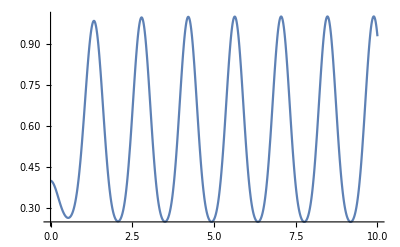

```mathematica
Plot[Fid3[a],{a,0,10}]
```

```mathematica
Fid4[a_]:=(2+Abs[Exp[ⅈ *π*a/Sqrt[2]]*(Cos[Sqrt[(π*0.5)^2*(2*a^2+1)]]+ⅈ*0.5*((2*Sqrt[2]*a^2)/(2*Sqrt[2]*a^2+1))^0.5*Sin[Sqrt[(π*0.5)^2*(2*a^2+1)]])+Exp[-ⅈ *π*a/Sqrt[2]]*(Cos[Sqrt[(π*0.5)^2*(2*a^2+1)]]-ⅈ*0.5*((2*Sqrt[2]*a^2)/(2*Sqrt[2]*a^2+1))^0.5*Sin[Sqrt[(π*0.5)^2*(2*a^2+1)]])]^2)/6
```

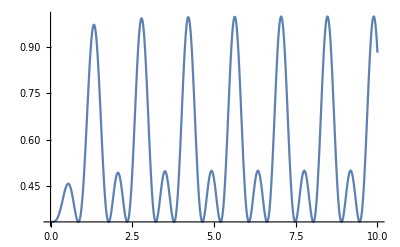

```mathematica
Plot[Fid4[a],{a,0,10}]
```

```mathematica
InFid1[a_]:=1-((((0.5*a^2+0.25)^-0.5*Sin[Sqrt[(π*0.5)^2*(2*a^2+1)]])^2))/4
```

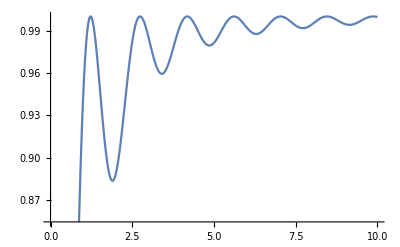

```mathematica
Plot[InFid1[a],{a,0,10}]
```

```mathematica
InFid2[a_]:=(0.05*(4+(0.5*a^2+0.25)^-1*(Sin[Sqrt[(π*0.5)^2*(2*a^2+1)]])^2+4*(0.5*a^2+0.25)^-0.5*Sin[Sqrt[(π*0.5)^2*(2*a^2+1)]]+4))
```

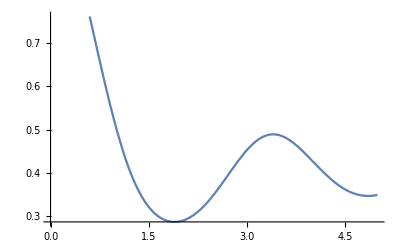

```mathematica
Plot[InFid2[a],{a,0,5}]
```